```mathematica
Secante[f_,a0_,b0_,xtol_,ytol_,Nmax_]:=
Module[{a,b,fa,fb,c,fc,n},
a=a0;
b=b0;
fa=f[a];
fb=f[b];
c=b-fb*(b-a)/(fb-fa);
fc=f[c];
n=1;
While[(Abs[b-c] ≥xtol) && (Abs[fc] ≥ytol) && (n≤Nmax),a=b;fa=fb;
b=c;fb=fc;
c=b-fb*(b-a)/(fb-fa);
fc=f[c];
n+=1];
{c,n}]
```

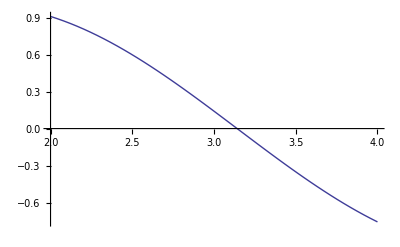

{3.14159,4}

```mathematica
f1[x_]:=Sin[x];Plot[f1[x],{x,2,4}]
Secante[f1,2.0,4.0,10^-6,10^-7,50]
```

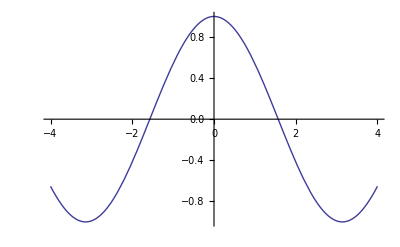

{-1.5708,5}

```mathematica
f2[x_]:=Cos[x];Plot[f2[x],{x,-4,4}]
Secante[f2,2.0,4.0,10^-6,10^-7,70]
```